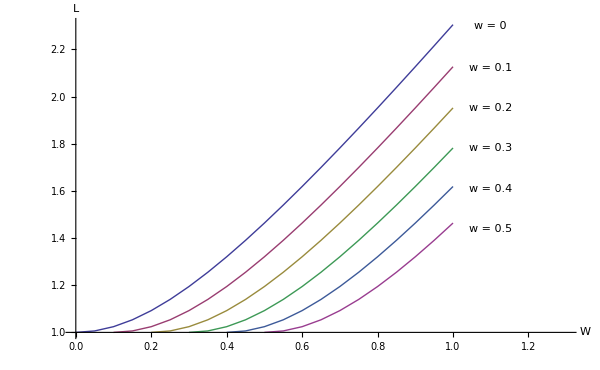

Hold[getLengthAnchor[P,W,0]]

{{{0.1,0.546192},{0.6,1.33495},{1.1,2.2878},{1.6,3.26634},{2.1,4.25384},{2.6,5.24558},{3.1,6.23967},{3.6,7.23521},{4.1,8.23172}},{{0.1,5.50448},{0.6,5.65811},{1.1,6.00811},{1.6,6.51225},{2.1,7.12954},{2.6,7.82834},{3.1,8.58625},{3.6,9.3878},{4.1,10.2222}},{{0.1,10.5023},{0.6,10.5841},{1.1,10.7788},{1.6,11.0779},{2.1,11.47},{2.6,11.9428},{3.1,12.4842},{3.6,13.0838},{4.1,13.7321}},{{0.1,15.5016},{0.6,15.5571},{1.1,15.6909},{1.6,15.8998},{2.1,16.1798},{2.6,16.5257},{3.1,16.9319},{3.6,17.3928},{4.1,17.9027}},{{0.1,20.5012},{0.6,20.5433},{1.1,20.6449},{1.6,20.8047},{2.1,21.0209},{2.6,21.2909},{3.1,21.6118},{3.6,21.9806},{4.1,22.3939}}}

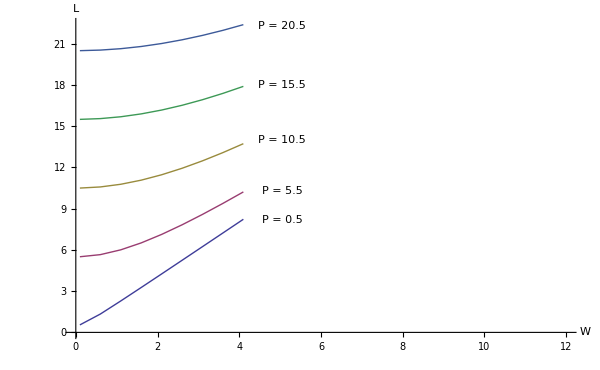

```mathematica
(*
P = 1;
A = 1;
l = 0.15;
w = 0.1;
*)

getLimits[P_,A_,l_,segWidth_]:=Module[{expr1, expr2, subs1, subs2, sol, xrule1, xrule2, xval1, xval2, yrule1, yrule2, yval1, yval2, angle, y, x},
Off[Reduce::ratnz];
Off[Reduce::incs];
expr1 = l^2 == (x-P/2)^2 + (y+A/2)^2;expr2 = y == A/2 * Cos[2*Pi*x/P];
subs1  = Solve[expr1, {y}];
subs2  = Solve[expr2, {y}]; sol =Reduce[expr1 && expr2  && x > 0 && x < P, {x,y}, Reals];xrule1=Solve[sol[[1]][[1]],x];
xrule2=Solve[sol[[2]][[1]],x];
xval1 =(x /. xrule1) [[1]];
xval2 =(x /. xrule2 )[[1]] ;yrule1 =Solve[sol[[1]][[2]] /. xrule1[[1]],y];yrule2 =Solve[sol[[2]][[2]] /. xrule2[[1]],y];yval1 =(y /. yrule1) [[1]];
yval2 =(y /. yrule2 )[[1]] ;
angle = ArcSin[(yval1+A/2)/l];
segWidth/2 * Cos[angle]]


getLength[P_,W_] := Module[{L}, 2*(P^2/4 + W^2)^(1/2)]

getLengthAnchor[P_, W_, segWidth_] := Module[{x},
Integrate[(((-(W-segWidth)Pi/P )*Sin[2Pi*x/P])^2+1)^(1/2),{ x, 0, P}]
]

(* continuum with segment width *)
results = {{{0.,1.},{0.05,1.0061402544253308},{0.1,1.024235228564182},{0.15000000000000002,1.0533960261691375},{0.2,1.0923835473311778},{0.25,1.1398386643694227},{0.30000000000000004,1.1944523009924373},{0.35000000000000003,1.255057045703324},{0.4,1.320658226693122},{0.45,1.3904299495666794},{0.5,1.4636954724135356},{0.55,1.5399031882599155},{0.6000000000000001,1.6186036276736517},{0.65,1.6994295473738867},{0.7000000000000001,1.782079525980375},{0.75,1.8663047918006948},{0.8,1.95189878007281},{0.8500000000000001,2.038688897811047},{0.9,2.1265300347065237},{0.9500000000000001,2.2152994397675827},{1.,2.3048926613536915}},{{0.1,1.},{0.15000000000000002,1.0061402544253308},{0.2,1.024235228564182},{0.25,1.0533960261691369},{0.30000000000000004,1.0923835473311778},{0.35000000000000003,1.1398386643694227},{0.4,1.1944523009924373},{0.45,1.255057045703324},{0.5,1.320658226693122},{0.55,1.3904299495666794},{0.6000000000000001,1.4636954724135363},{0.65,1.5399031882599155},{0.7000000000000001,1.6186036276736517},{0.75,1.6994295473738867},{0.8,1.782079525980375},{0.8500000000000001,1.8663047918006945},{0.9,1.95189878007281},{0.9500000000000001,2.038688897811047},{1.,2.1265300347065237}},{{0.2,1.},{0.25,1.0061402544253308},{0.30000000000000004,1.024235228564182},{0.35000000000000003,1.0533960261691375},{0.4,1.0923835473311778},{0.45,1.1398386643694227},{0.5,1.1944523009924373},{0.55,1.255057045703324},{0.6000000000000001,1.320658226693122},{0.65,1.3904299495666794},{0.7000000000000001,1.4636954724135356},{0.75,1.5399031882599155},{0.8,1.6186036276736517},{0.8500000000000001,1.6994295473738865},{0.9,1.7820795259803746},{0.9500000000000001,1.8663047918006948},{1.,1.95189878007281}},{{0.30000000000000004,1.},{0.35000000000000003,1.0061402544253308},{0.4,1.024235228564182},{0.45000000000000007,1.0533960261691375},{0.5,1.0923835473311776},{0.55,1.1398386643694227},{0.6000000000000001,1.1944523009924373},{0.65,1.255057045703324},{0.7000000000000001,1.320658226693122},{0.7500000000000001,1.3904299495666794},{0.8,1.4636954724135356},{0.8500000000000001,1.5399031882599155},{0.9000000000000001,1.6186036276736517},{0.9500000000000001,1.6994295473738867},{1.,1.7820795259803746}},{{0.4,1.},{0.45,1.0061402544253308},{0.5,1.024235228564182},{0.55,1.0533960261691375},{0.6000000000000001,1.0923835473311778},{0.65,1.1398386643694227},{0.7000000000000001,1.1944523009924373},{0.75,1.255057045703324},{0.8,1.320658226693122},{0.8500000000000001,1.3904299495666794},{0.9,1.4636954724135356},{0.9500000000000001,1.5399031882599155},{1.,1.6186036276736517}},{{0.5,1.},{0.55,1.0061402544253308},{0.6,1.024235228564182},{0.65,1.0533960261691375},{0.7,1.0923835473311776},{0.75,1.1398386643694227},{0.8,1.1944523009924373},{0.85,1.255057045703324},{0.9,1.320658226693122},{0.9500000000000001,1.3904299495666794},{1.,1.4636954724135356}}};

graphResult = ListLinePlot[results,
 AxesLabel->{Style["W",20],Style["L",20]},
PlotRange->{{0,1.3},Automatic},
ImageSize->600,
Epilog->{Style[Text["w = 0",{1.1,2.3}],20],
Style[Text["w = 0.1",{1.1,2.12}],20],
Style[Text["w = 0.2",{1.1,1.95}],20],
Style[Text["w = 0.3",{1.1,1.78}],20],
Style[Text["w = 0.4",{1.1,1.61}],20],
Style[Text["w = 0.5",{1.1,1.44}],20]

}]

(* getLengthAnchor[P_, W_, segWidth_] *)

(*
expr = getLengthAnchor[1,Z,V]
results = Table[{Z, expr} ,{V,0, 0.5, 0.1}, {Z, V,1, 0.05}]
graphResult = ListLinePlot[results,PlotLabel->Style["Required Snake Length for Given Wall Width",20], AxesLabel->{Style["wall width",15],Style["snake length",15]},
PlotRange->{{0,1.3},Automatic},
ImageSize->600,
Epilog->{Style[Text["seg width = 0",{1.15,2.3}],15],
Style[Text["seg width = 0.1",{1.15,2.12}],15],
Style[Text["seg width = 0.2",{1.15,1.95}],15],
Style[Text["seg width = 0.3",{1.15,1.78}],15],
Style[Text["seg width = 0.4",{1.15,1.61}],15],
Style[Text["seg width = 0.5",{1.15,1.44}],15]

}]
*)
(*
expr = getLengthAnchor[1,W,w]
results = Table[{W, expr} /. {w->V , W->Z},{V,0, 0.5, 0.1}, {Z, V,1, 0.05}]
graphResult = ListLinePlot[results,PlotLabel->Style["Required Snake Length for Given Wall Width",20], AxesLabel->{Style["wall width",15],Style["snake length",15]},
PlotRange->{{0,1.3},Automatic},
ImageSize->600,
Epilog->{Style[Text["seg width = 0",{1.15,2.3}],15],
Style[Text["seg width = 0.1",{1.15,2.12}],15],
Style[Text["seg width = 0.2",{1.15,1.95}],15],
Style[Text["seg width = 0.3",{1.15,1.78}],15],
Style[Text["seg width = 0.4",{1.15,1.61}],15],
Style[Text["seg width = 0.5",{1.15,1.44}],15]

}]
*)



expr = Hold[getLengthAnchor[P,W,0]]
(*expr = Hold[expr]*)

(*results = {{{0.5,1.1524463306768455},{1.,2.0941376018492153},{1.5,3.069668441399165},{2.,4.0559143094198},{2.5,5.047000333101229},{3.,6.0407102437312385}}}*)

(*results = Table[{W, Re[ReleaseHold[expr]]}  /. {P->V , W->Z},{V,0.5, 20.5, 5}, {Z, 0.1,4.1, 0.5}] *)

(*
results = {{{0.1,0.5461917736655888},{3.1,6.239665500278879},{6.1,12.222972069785033},{9.1,18.21651275539472}},{{0.1,2.5098405723074664},{3.1,6.859821102859392},{6.1,12.606672560867803},{9.1,18.500628732762895}},{{0.1,4.505478112949167},{3.1,7.93605912569356},{6.1,13.317068327340731},{9.1,19.04044980397598}},{{0.1,6.503794340659493},{3.1,9.29164765343572},{6.1,14.265793962653696},{9.1,19.77780760850323}},{{0.1,8.502902081741547},{3.1,10.827919804190325},{6.1,15.3989200648523},{9.1,20.677177986951396}},{{0.1,10.502349511524168},{3.1,12.484245745018308},{6.1,16.67771230826659},{9.1,21.712519245144982}}}*)

(* results = {{{0.1,0.5461917736655888},{3.,6.0407102437312385}},{{0.1,1.0242352285641823},{3.,6.13933688279833}},{{0.1,1.516316465247536},{3.,6.282412805547647}},{{0.1,2.0122805088506612},{3.,6.462613855640651}}}
*)

(* continuum snake, no width *)
results = {{{0.1,0.5461917736655888},{0.6,1.3349455560025376},{1.1,2.2877995270436173},{1.6,3.266342355012633},{2.1,4.253842610707104},{2.6,5.24557581303505},{3.1,6.239665500278879},{3.6,7.235210437509745},{4.1,8.231721110970986}},{{0.1,5.504483443109508},{0.6,5.658109486118378},{1.1,6.00810951032148},{1.6,6.512247324124148},{2.1,7.129543958100504},{2.6,7.828343215861693},{3.1,8.58625090888982},{3.6,9.387795385202237},{4.1,10.222237037605078}},{{0.1,10.502349511524168},{0.6,10.584092170049757},{1.1,10.778809894394437},{1.6,11.077923952873755},{2.1,11.470027246977368},{2.6,11.9427699817936},{3.1,12.484245745018308},{3.6,13.083756179729304},{4.1,13.732090717636197}},{{0.1,15.501591749082987},{0.6,15.557149441963269},{1.1,15.69085745957214},{1.6,15.899816534661145},{2.1,16.179808840110947},{2.6,16.52571662882036},{3.1,16.931944983633255},{3.6,17.39278413224876},{4.1,17.902680560603475}},{{0.1,20.501203557297583},{0.6,20.543261522876918},{1.1,20.644869914119795},{1.6,20.80473505574912},{2.1,21.020905719759508},{2.6,21.290896234451754},{3.1,21.61182728395705},{3.6,21.980567511161084},{4.1,22.393862720289132}}}

graphResult = ListLinePlot[results,
 AxesLabel->{Style["W  ",20],Style["L",20]},
PlotRange->{{0,12},Automatic},
ImageSize->600,
Epilog->{
Style[Text["P = 0.5",{5.05,8.2}],20],
Style[Text["P = 5.5",{5.05,10.3}],20],
Style[Text["P = 10.5",{5.05,14}],20],
Style[Text["P = 15.5",{5.05,18}],20],
Style[Text["P = 20.5",{5.05,22.3}],20]

}
]


(*
expr = Hold[getLengthAnchor[1,W,w]]
results = Table[expr  /. w->V ,{V,0, 0.5, 0.05}]

Plot[ReleaseHold[results], {W, 0, 2}]
*)
(*
expr = Hold[{y, getLengthAnchor[1,y,0]}]
results = Table[expr /. y ->  x, {x,0, 2, 0.05}];
results2 = ReleaseHold[results]
graphResult = ListLinePlot[results2]
*)
(*
expr = getLength[1,x]
Plot[expr, {x,0,2}]
*)

(*
getLimits[1,1,0.15,0.1];
getLimits[1,1,0.15,0.15];

expr = getLimits[1,1,0.15,x];
Plot[expr, {x,0.0,1.0}];

expr = Hold[{y, getLimits[1,1,y,0.1]}];

results = Table[expr /. y ->  x, {x,0.05, 1.05, 0.05}];
results2 = ReleaseHold[results];

graphResult = ListLinePlot[results2];
graphResult
*)

(* vals  = Range[0.01, 0.02, 0.001] *)

(* expr = getLimits[1,1,vals,0.1] *)

(* Plot[expr, {x,0.01,0.02}] *)




(* Plot[{y /. subs2, y /. subs1[[2]], y /. subs1[[1]]}, {x,0,P}] *)



(* x values in rule form *)





(* y values in rule form *)





(* angle = ArcCos[(xval2-P/2)/l]; *)

(* If[xval1 > xval2, v = 1, v =0] *)

(* lower and upper limit of distance from curve to the wall with a given robot configuration of l, w, and curve paramters of A and P *)
```